0.95

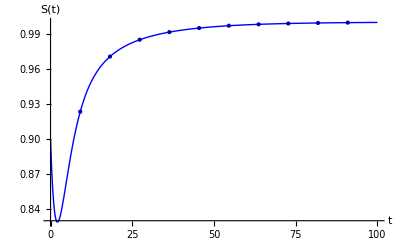

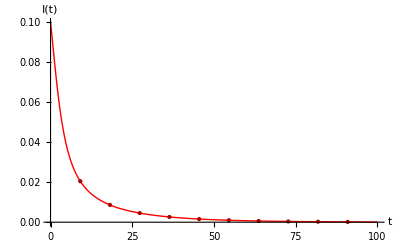

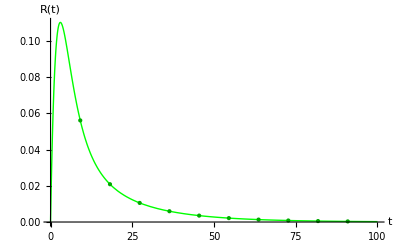

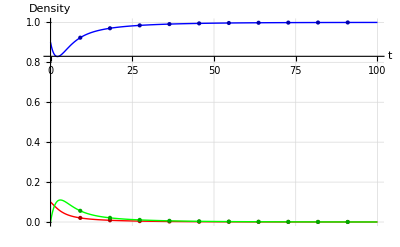

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]* i[t]/n+ν r[t];
eq2=β*s[t]*i[t]/n-γ*i[t];
eq3=γ*i[t]-ν r[t];
n=1;
β=0.95;
γ=1.0;
ν=0.5;
R0=N[β/γ]
tf=100;
szero=0.90;
izero=0.1;
rzero=0.0;

sol=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3,s[0]==szero,i[0]==izero,r[0]==rzero},{s,i,r},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For I[t] versus t *)
plot2a=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"R"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For R[t] versus t *)
plot3a=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"},{Graphics[{Green,Line[{{0,0},{1,0}}]}],"R(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[i[t]/.sol],Evaluate[r[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","I(t)","R(t)"}, PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

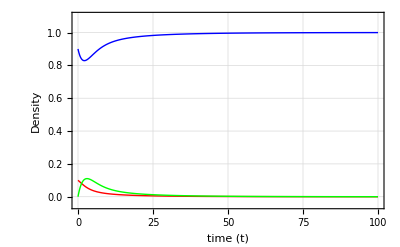

3.

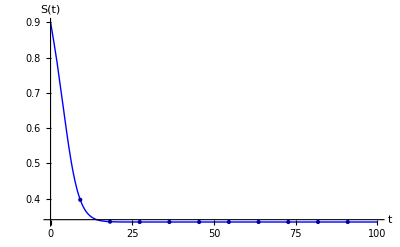

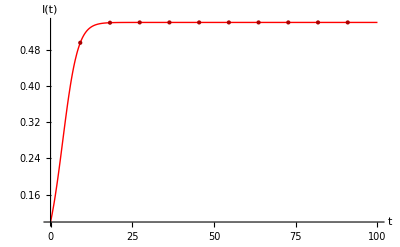

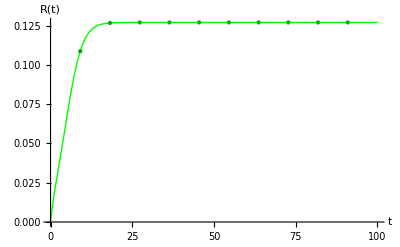

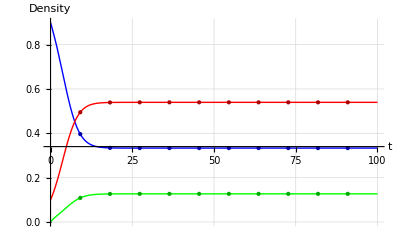

```mathematica
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]* i[t]/n+ν r[t];
eq2=β*s[t]*i[t]/n-γ*i[t];
eq3=γ*i[t]-ν r[t];
n=1;
β=0.6;
γ=0.2;
ν=0.85;
R0=N[β/γ]
tf=100;
szero=0.90;
izero=0.1;
rzero=0.0;

sol=NDSolve[{s'[t]==eq1,i'[t]==eq2,r'[t]==eq3,s[0]==szero,i[0]==izero,r[0]==rzero},{s,i,r},{t,tf}];

plot1=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"S"[t]},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue]      (* For S[t] versus t *)
plot1a=Plot[a[t]=Evaluate[s[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Blue,Mesh->10,MeshStyle->Darker@Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]; (* For S[t] versus t *)


plot2=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"I"[t]},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red]    (* For I[t] versus t *)
plot2a=Plot[b[t]=Evaluate[i[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Red,Mesh->10,MeshStyle->Darker@Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]] ;


plot3=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"R"[t]},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green]    (* For R[t] versus t *)
plot3a=Plot[c[t]=Evaluate[r[t]/.sol],{t,0,tf},PlotRange->All,AxesLabel->{t,"Density"},PlotStyle->Green,Mesh->10,MeshStyle->Darker@Green,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]];


ShowLegend[Show[plot1a ,plot2a,plot3a],{{{Graphics[{Blue,Line[{{0,0},{1,0}}]}],"S(t)"},{Graphics[{Red,Line[{{0,0},{1,0}}]}],"I(t)"},{Graphics[{Green,Line[{{0,0},{1,0}}]}],"R(t)"}},LegendShadow->None,LegendSpacing->0,LegendSize-> {0.5,0.5}}]

plotall=Plot[{Evaluate[s[t]/.sol],Evaluate[i[t]/.sol],Evaluate[r[t]/.sol]},{t,0,tf},PlotRange->{{0,tf},{-0.05,1.1}},PlotLegend->{"S(t)","I(t)","R(t)"}, PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},LegendShadow->None,LegendSpacing->0,LegendPosition->{0.2,0},LegendSize-> {0.2,0.3},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Density ",""},{"time "[t],""}}]

(*plotP=ParametricPlot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"E"[t]}]
plotQ=ParametricPlot[Evaluate[{x2[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{"E"[t],"I"[t]}]
plotR=ParametricPlot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,tf},PlotRange->All,AxesLabel->{S[t],"I"[t]}]
h1[t_]:=Evaluate[x1[t]/.sol]
h2[t_]:=Evaluate[x2[t]/.sol]
h3[t_]:=Evaluate[x3[t]/.sol]*)
```

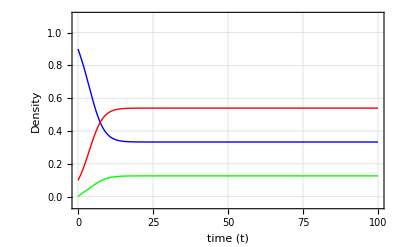

1.

0.95

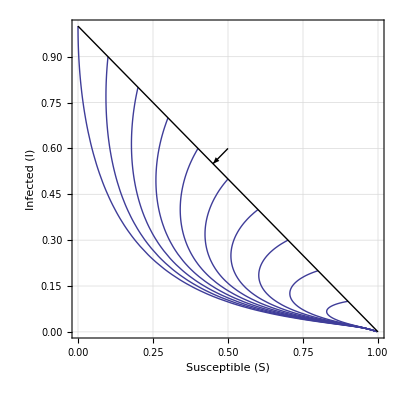

```mathematica
(*This is example of Tunnel Diode Example*)
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]*i[t]/n+ν (n-s[t]-i[t]);
eq2=β*s[t]*i[t]/n-γ*i[t];

n=1;
β=0.95;
γ=1.0;
ν=0.5;
R0=N[β/γ]
St=n/R0;
It=(n μ (R0-1))/β;
tf=50;
num=10;

szero[0]=1.0;
izero[0]=0.0;
rzero[0]=0.0;

szero[1]=0.9;
izero[1]=0.1;
rzero[1]=0.0;

szero[2]=0.8;
izero[2]=0.2;
rzero[2]=0.0;

szero[3]=0.7;
izero[3]=0.3;
rzero[3]=0.0;

szero[4]=0.6;
izero[4]=0.4;
rzero[4]=0.0;

szero[5]=0.5;
izero[5]=0.5;
rzero[5]=0.0;

szero[6]=0.4;
izero[6]=0.6;
rzero[6]=0.0;

szero[7]=0.3;
izero[7]=0.7;
rzero[7]=0.0;

szero[8]=0.2;
izero[8]=0.8;
rzero[8]=0.0;

szero[9]=0.1;
izero[9]=0.9;
rzero[9]=0.0;

szero[10]=0.0;
izero[10]=1.0;
rzero[10]=0.0;


Do[sol[k]=NDSolve[{s'[t]==eq1,i'[t]==eq2, s[0]==szero[k],i[0]==izero[k]},{s,i},{t,tf}],{k,0,num}]


pl[k_]:=ParametricPlot[Evaluate[{s[t],i[t]}/.sol[k]],{t,0,tf},PlotRange->All]

pls=Flatten[Table[pl[k],{k,0,num}]];
line = Graphics[Line[{{0,1.0},{1.0,0}}]];
arrow=Graphics[{Arrowheads[0.03],Arrow[{{0.5,0.6},{0.45,0.55}}]}];
pic1=Show[pls,line,arrow,PlotRange->{{0.0,1.0},{0.0,1.0}},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

0.2

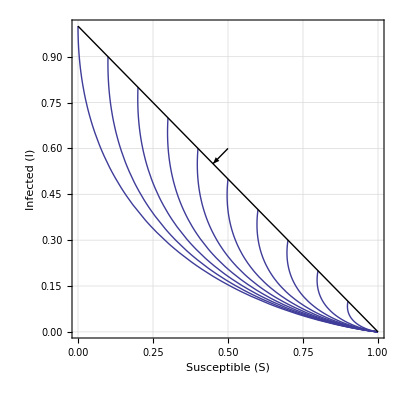

```mathematica
(*This is example of Tunnel Diode Example*)
Clear["Global`*"]
Needs["PlotLegends`"]
eq1=-β * s[t]*i[t]/n+ν (n-s[t]-i[t]);
eq2=β*s[t]*i[t]/n-γ*i[t];

n=1;
β=0.1;
γ=0.5;
ν=0.4;
R0=N[β/γ]
St=n/R0;
It=(n μ (R0-1))/β;
tf=50;
num=10;

szero[0]=1.0;
izero[0]=0.0;
rzero[0]=0.0;

szero[1]=0.9;
izero[1]=0.1;
rzero[1]=0.0;

szero[2]=0.8;
izero[2]=0.2;
rzero[2]=0.0;

szero[3]=0.7;
izero[3]=0.3;
rzero[3]=0.0;

szero[4]=0.6;
izero[4]=0.4;
rzero[4]=0.0;

szero[5]=0.5;
izero[5]=0.5;
rzero[5]=0.0;

szero[6]=0.4;
izero[6]=0.6;
rzero[6]=0.0;

szero[7]=0.3;
izero[7]=0.7;
rzero[7]=0.0;

szero[8]=0.2;
izero[8]=0.8;
rzero[8]=0.0;

szero[9]=0.1;
izero[9]=0.9;
rzero[9]=0.0;

szero[10]=0.0;
izero[10]=1.0;
rzero[10]=0.0;


Do[sol[k]=NDSolve[{s'[t]==eq1,i'[t]==eq2, s[0]==szero[k],i[0]==izero[k]},{s,i},{t,tf}],{k,0,num}]


pl[k_]:=ParametricPlot[Evaluate[{s[t],i[t]}/.sol[k]],{t,0,tf},PlotRange->All]

pls=Flatten[Table[pl[k],{k,0,num}]];
line = Graphics[Line[{{0,1.0},{1.0,0}}]];
arrow=Graphics[{Arrowheads[0.03],Arrow[{{0.5,0.6},{0.45,0.55}}]}];
pic1=Show[pls,line,arrow,PlotRange->{{0.0,1.0},{0.0,1.0}},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Frame->{True,True,True,True},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

-0.768

-0.48

0.811264

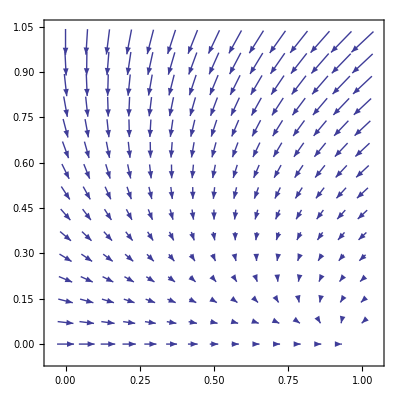

```mathematica
Clear["Global`*"]
β=0.12;
γ=0.6;
ν=0.4;

ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;

VectorPlot[{-β s i/n+ν (n-s-i), β s i/n-γ i},{s,0,1},{i,0,1}]
```

0.95

-0.05

0.866386

{1,0}

{1.05263,-0.0175439}

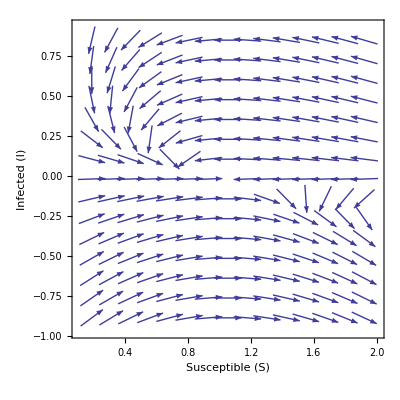

```mathematica
Clear["Global`*"]
β=0.95;
γ=1.0;
ν=0.5;

λ1=-(-ν(β+ν)+√(ν^2(β+ν)^2-4ν(β-γ)(γ+ν)^2))/(2(γ+ν));
λ2=-(-ν(β+ν)-√(ν^2(β+ν)^2-4ν(β-γ)(γ+ν)^2))/(2(γ+ν));
r0=β/γ
diff=β-γ
ξ=ν^2(β+ν)^2-4ν(β-γ)(γ+ν)^2;
ξ=√ξ
e1={1,0}
e2={1/r0, γ ν(r0-1)/(β(γ+ν))}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)
δ=ξ;
VectorPlot[{-β s i/1+ν (1-s-i), β s i/1-γ i},{s,e2[[1]]-δ,e2[[1]]+δ},{i,e2[[2]]-δ,e2[[2]]+δ},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

```mathematica
?Print
```

Print[expr] prints expr as output.

Thi sucks

3.

0.4

0.0196562

1.4994

1.51906

{1,0}

{0.333333,0.539683}

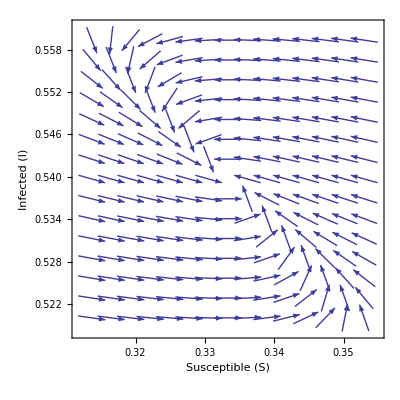

```mathematica
Clear["Global`*"]
β=0.6;
γ=0.2;
ν=0.85;

λ1=-(-ν(β+ν)+√(ν^2(β+ν)^2-4ν(β-γ)(γ+ν)^2))/(2(γ+ν));
λ2=-(-ν(β+ν)-√(ν^2(β+ν)^2-4ν(β-γ)(γ+ν)^2))/(2(γ+ν));
r0=β/γ
diff=β-γ
δ=ν^2(β+ν)^2-4ν(β-γ)(γ+ν)^2
ζ=4ν(β-γ)(γ+ν)^2
c=ν(β+ν);
c=c^2
e1={1,0}
e2={1/r0, γ ν(r0-1)/(β(γ+ν))}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)

VectorPlot[{-β s i/1+ν (1-s-i), β s i/1-γ i},{s,e2[[1]]-δ,e2[[1]]+δ},{i,e2[[2]]-δ,e2[[2]]+δ},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```

2.

0.35

-0.0695938

0.126

0.0564063

{1,0}

{0.5,0.208333}

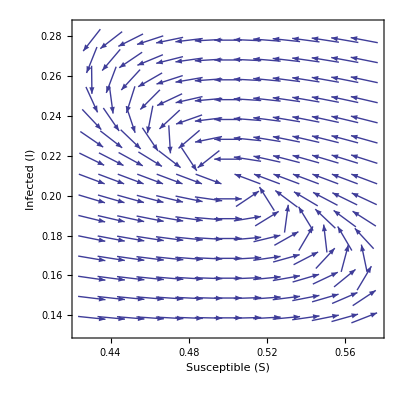

```mathematica
Clear["Global`*"]
β=0.7;
γ=0.35;
ν=0.25;

λ1=-(-ν(β+ν)+√(ν^2(β+ν)^2-4ν(β-γ)(γ+ν)^2))/(2(γ+ν));
λ2=-(-ν(β+ν)-√(ν^2(β+ν)^2-4ν(β-γ)(γ+ν)^2))/(2(γ+ν));
r0=β/γ
diff=β-γ
δ=ν^2(β+ν)^2-4ν(β-γ)(γ+ν)^2
ζ=4ν(β-γ)(γ+ν)^2
c=ν(β+ν);
c=c^2
e1={1,0}
e2={1/r0, γ ν(r0-1)/(β(γ+ν))}
(*ζ=4 ν (β-γ)(γ+ν)^2
diff=β-γ
δ=N[ν^2 (β+ν)^2-4 ν (β-γ)(γ+ν)^2]
λ1=-ν(β+ν)
n=1;
*)

VectorPlot[{-β s i/1+ν (1-s-i), β s i/1-γ i},{s,e2[[1]]-δ,e2[[1]]+δ},{i,e2[[2]]-δ,e2[[2]]+δ},VectorScale->{Automatic,Automatic,None},FrameLabel->{{"Infected (
StyleBox[\"I\",\nFontSlant->\"Italic\"])",""},{"Susceptible "[S],""}}]
```